```mathematica
Clear["Global`*"]
Column@NotebookEvaluate[FileNameJoin[{NotebookDirectory[],"../../../mathematica_plot_options.nb"}]]

Tlist=Table[t,{t,0.5,0.57,0.01}];

Table[name[t]=FileNameJoin[{"/Volumes/home/BEM/Tonegawa/Tonegawa2024_T"<>StringReplace[ToString[t],"."->"d"]<>"_DT0d025_ELEMlinear_ALEquasi_quad_ALEPERIOD1_B10d125/result.json"}],{t,Tlist}]
Do[data[t]=Import@name[t],{t,Tlist}]
jsonInfo[name[Last[Tlist]]]
```

plot2Doption
plot3Doption
framelabel[xlabel_String,ylabel_String,size_:20]
axeslabel2D[xlabel_String,ylabel_String,size_:20]
axeslabel3D[xlabel_String,ylabel_String,zlabel_String,size_:20]
axeslabel[labels_List,size_: 20]
importData
jsonInfo
interpolateAndFourier
interpolateAndFourierTr
MyFourier[list_,n_]
MyInverseFourier[list_,n_]
MyDiscreteConvolve[f_,g_]
MyDiscreteConvolveUsingCn[FourierGF_]
Rv[q_]
Rs[q_]
W2dQdt[q_,w_]
Q2Roll[{a_,b_,c_,d_}]
Q2Pitch[{a_,b_,c_,d_}]
Q2Yaw[{a_,b_,c_,d_}]
getOmegaFromKandDepth
getTFromLandDepth

{/Volumes/home/BEM/Tonegawa/Tonegawa2024_T0d5_DT0d025_ELEMlinear_ALEquasi_quad_ALEPERIOD1_B10d125/result.json,/Volumes/home/BEM/Tonegawa/Tonegawa2024_T0d51_DT0d025_ELEMlinear_ALEquasi_quad_ALEPERIOD1_B10d125/result.json,/Volumes/home/BEM/Tonegawa/Tonegawa2024_T0d52_DT0d025_ELEMlinear_ALEquasi_quad_ALEPERIOD1_B10d125/result.json,/Volumes/home/BEM/Tonegawa/Tonegawa2024_T0d53_DT0d025_ELEMlinear_ALEquasi_quad_ALEPERIOD1_B10d125/result.json,/Volumes/home/BEM/Tonegawa/Tonegawa2024_T0d54_DT0d025_ELEMlinear_ALEquasi_quad_ALEPERIOD1_B10d125/result.json,/Volumes/home/BEM/Tonegawa/Tonegawa2024_T0d55_DT0d025_ELEMlinear_ALEquasi_quad_ALEPERIOD1_B10d125/result.json,/Volumes/home/BEM/Tonegawa/Tonegawa2024_T0d56_DT0d025_ELEMlinear_ALEquasi_quad_ALEPERIOD1_B10d125/result.json,/Volumes/home/BEM/Tonegawa/Tonegawa2024_T0d57_DT0d025_ELEMlinear_ALEquasi_quad_ALEPERIOD1_B10d125/result.json}

no. | title | length
1 | cpu_time | 251
2 | eq_of_motion | 251
3 | float_COM | 251
4 | float_EK | 251
5 | float_EP | 251
6 | float_accel | 251
7 | float_area | 251
8 | float_drag_force | 251
9 | float_drag_torque | 251
10 | float_force | 251
11 | float_pitch | 251
12 | float_roll | 251
13 | float_torque | 251
14 | float_velocity | 251
15 | float_yaw | 251
16 | gradPhi_worst_grad | 251
17 | gradPhi_worst_iteration | 251
18 | gradPhi_worst_value | 251
19 | simulation_time | 251
20 | wall_clock_time | 251
21 | water_E | 251
22 | water_EK | 251
23 | water_EP | 251
24 | water_face_size | 251
25 | water_point_size | 251
26 | water_volume | 251

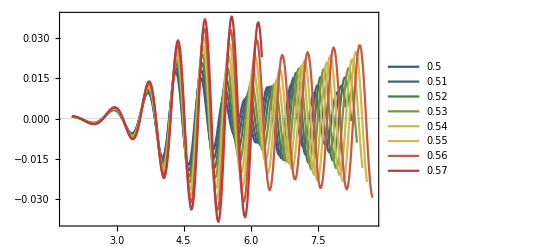

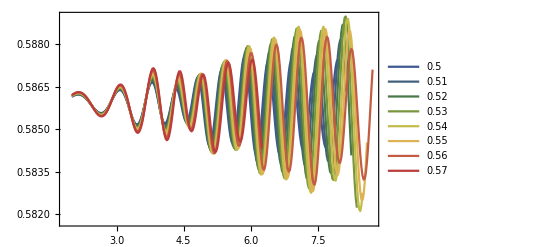

```mathematica
findFirst[data_,condition_]:=Module[{list,ret},
list="simulation_time"/.data;
ret=Length[list];
Return [ret];
]

indices[data_,{s_,e_}_:{5,10}]:=Module[{list,len,startIndex,endIndex},
list="simulation_time"/.data;
len=Length[list];
startIndex=Position[list,x_/;x>s];
If[startIndex=={},startIndex=len,startIndex=startIndex[[1,1]]];
endIndex=Position[list,x_/;x>e];
If[endIndex=={},endIndex=len,endIndex=endIndex[[1,1]]];
startIndex;;endIndex
];

extractFourier[dataIN_,{s_,e_}_:{5,10},title_:"float_pitch",n_:0]:=Module[{end,data,x,y,span},
span=indices[dataIN,{s,e}];
x=("simulation_time"/.dataIN)[[span]];
If[n==0,y=(title/.dataIN)[[span]],y=((title/.dataIN)[[span]])[[;;,n]]];
interpolateAndFourier[x,y]
]

color[T_]:=ColorData[{"DarkRainbow",MinMax[Tlist]}][T];

a=12;

ListPlot[Table[Transpose[{("simulation_time"/.data[T]),("float_pitch"/.data[T])}][[indices[data[T],{2,2+a*T}]]],{T,Tlist}]
,PlotLegends->Tlist
,Evaluate[plot2Doption]
,PlotStyle->Table[{color[T]},{T,Tlist}]
,Joined->True
,PlotRange->All]
ListPlot[Table[Transpose[{("simulation_time"/.data[T]),("float_COM"/.data[T])[[;;,3]]}][[indices[data[T],{2,2+a*T}]]],{T,Tlist}]
,PlotLegends->Tlist
,Evaluate[plot2Doption]
,PlotStyle->Table[{color[T]},{T,Tlist}]
,Joined->True
,PlotRange->All]
```

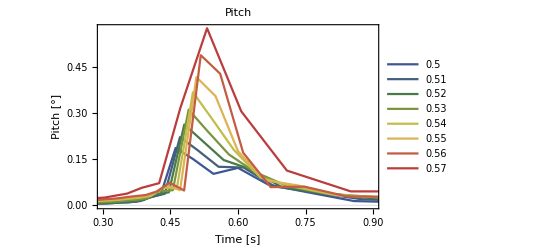

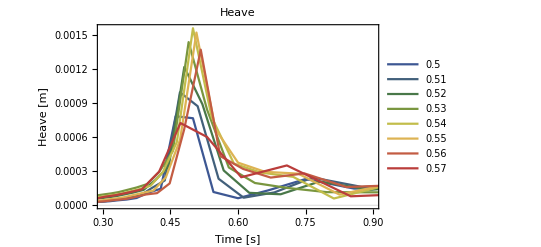

図の見た方：浮体のピッチは単純なsin関数ではなく，様々な周期のsin,cos関数の和となっている．この図は，ある入射波に対するピッチ動揺において，よく揺れた成分を示している

```mathematica
legend={};
ListPlot[
Table[AppendTo[legend,T];{1/#1,180/(2π)#2}&@@@extractFourier[data[T],{2,2+a*T},"float_pitch"][[2;;]],{T,Tlist}]
,Joined->True
,PlotRange->{{0.3,0.9},All}
,Evaluate[plot2Doption]
,PlotLabel->"Pitch"
,FrameLabel->{"Time [s]","Pitch [°]"}
,PlotStyle->Table[{color[T]},{T,Tlist}]
,PlotLegends->legend]

ListPlot[
Table[{1/#1,#2}&@@@extractFourier[data[T],{2,2+a*T},"float_COM",3][[2;;]],{T,Tlist}]
,Joined->True
,PlotRange->{{0.3,0.9},All}
,Evaluate[plot2Doption]
,PlotLabel->"Heave"
,FrameLabel->{"Time [s]","Heave [m]"}
,PlotStyle->Table[{color[T]},{T,Tlist}]
,PlotLegends->legend
]

Print["図の見た方：浮体のピッチは単純なsin関数ではなく，様々な周期のsin,cos関数の和となっている．この図は，:3042:308b:5165:5c04:6ce2:306b:5bfe:3059:308b:30d4:30c3:30c1:52d5:63faにおいて，よく揺れた成分を示している"]
```

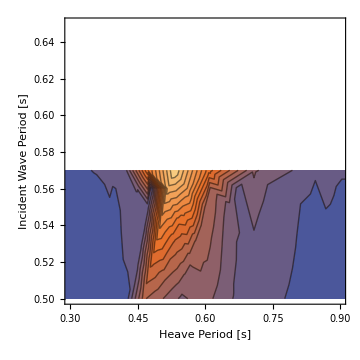

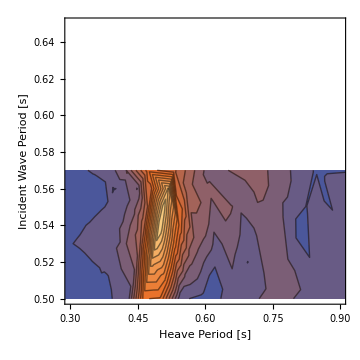

```mathematica
legend={};
ListContourPlot[
Flatten[Table[AppendTo[legend,T];{1/#1,T,180/(2π)#2}&@@@extractFourier[data[T],{2,2+a*T},"float_pitch"][[2;;]],{T,Tlist}],1]
,PlotRange->{{0.3,0.9},{0.5,0.65},All}
,FrameLabel->{"Heave Period [s]","Incident Wave Period [s]"}
,ImageSize->Medium
,Evaluate[plot3Doption]
,Contours->15
]


ListContourPlot[
Flatten[Table[{1/#1,T,#2}&@@@extractFourier[data[T],{2,2+a*T},"float_COM",3][[2;;]],{T,Tlist}],1]
,PlotRange->{{0.3,0.9},{0.5,0.65},All}
,FrameLabel->{"Heave Period [s]","Incident Wave Period [s]"}
,Evaluate[plot3Doption]
,ImageSize->Medium
,InterpolationOrder->3
,Contours->15]
```